Вводим начальный массив измерений

```mathematica
A=({{0, 0.88}, {0.2, 0.8}, {0.4, 0.840}, {0.6, 0.930}, {0.8, 0.980}, {1, 1.330}, {1.2, 1.799}, {1.4, 2.459}, {1.6, 3.249}, {1.8, 3.719}, {2, 3.929}, {2.2, 4.219}, {2.3, 4.279}, {2.4, 4.489}, {2.5, 4.539}, {2.6, 4.199}, {2.7, 4.029}, {2.8, 4.239}, {2.9, 3.719}, {3, 3.289}, {3.1, 2.559}, {3.2, 2.259}, {3.4, 1.739}, {3.6, 1.370}, {3.8, 1.290}, {3.85, 1.999}, {3.9, 3.449}, {3.95, 4.739}, {4, 6.038}, {4.2, 4.699}, {4.25, 4.659}, {4.3, 3.469}, {4.35, 2.159}, {4.4, 1.530}, {4.5, 0.8}, {4.6, 0.43}});
```

Добавдяем столбец значений с учетом фона

```mathematica
A=Transpose[A];
AppendTo[A,(A[[2,All]]-0.8098)]
```

{{0,0.2,0.4,0.6,0.8,1,1.2,1.4,1.6,1.8,2,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3,3.1,3.2,3.4,3.6,3.8,3.85,3.9,3.95,4,4.2,4.25,4.3,4.35,4.4,4.5,4.6},{0.88,0.8,0.84,0.93,0.98,1.33,1.799,2.459,3.249,3.719,3.929,4.219,4.279,4.489,4.539,4.199,4.029,4.239,3.719,3.289,2.559,2.259,1.739,1.37,1.29,1.999,3.449,4.739,6.038,4.699,4.659,3.469,2.159,1.53,0.8,0.43},{0.0702,-0.0098,0.0302,0.1202,0.1702,0.5202,0.9892,1.6492,2.4392,2.9092,3.1192,3.4092,3.4692,3.6792,3.7292,3.3892,3.2192,3.4292,2.9092,2.4792,1.7492,1.4492,0.9292,0.5602,0.4802,1.1892,2.6392,3.9292,5.2282,3.8892,3.8492,2.6592,1.3492,0.7202,-0.0098,-0.3798}}

Построим график по первым двум столбцам

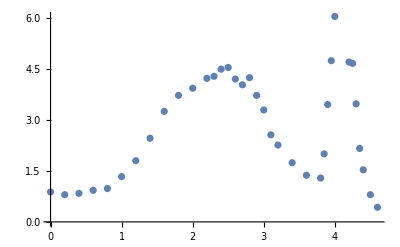

```mathematica
ListPlot[Transpose[A][[All,1;;2]]]
```

Введем функцию перевод энергии в импульс

```mathematica
p[Energy_]:=UnitConvert[(p/.(Solve[Energy==c √(p^2+m^2 c^2)-m c^2,p][[2]][[1]]))/.{m-> Quantity[1,"ElectronMass"],c-> Quantity[1,"SpeedOfLight"]}];
```

```mathematica
MkFermi[n_,nb_,p_]:=(√(n-nb))/p^(3/2)*10^6;
```

Энергия электронов внутренней конверсии ^137Cs 634 кэВ, тогда

```mathematica
CsElectronEnergy=UnitConvert[p[Quantity[634,"Kiloelectronvolts"]],"Kiloelectronvolts"/"SpeedOfLight"]
```

1024.648 keV/c

Теперь надо найти такой коэффициент k в формуле p=k I, чтобы пик внутренней конверсии выпал на полученное значение импульса. Значение возьмем чуть правее пиковой точки - 4.16 А.

```mathematica
k=CsElectronEnergy/Quantity[4.16,"Amperes"]
```

246.31 keV/(A c)

Чтобы сэкономить немного времени при работе с порядками, в исходной матрице проставим размерность у первого столбца

```mathematica
For[i=1,i≤ Length[A[[1]]],i++,
A[[1,i]]=Quantity[A[[1,i]],"Amperes"]
]
```

Теперь можем добавить еще один столбец для импульсов

```mathematica
AppendTo[A,A[[1,All]]*k]
```

{{0 A,0.2 A,0.4 A,0.6 A,0.8 A,1 A,1.2 A,1.4 A,1.6 A,1.8 A,2 A,2.2 A,2.3 A,2.4 A,2.5 A,2.6 A,2.7 A,2.8 A,2.9 A,3 A,3.1 A,3.2 A,3.4 A,3.6 A,3.8 A,3.85 A,3.9 A,3.95 A,4 A,4.2 A,4.25 A,4.3 A,4.35 A,4.4 A,4.5 A,4.6 A},{0.88,0.8,0.84,0.93,0.98,1.33,1.799,2.459,3.249,3.719,3.929,4.219,4.279,4.489,4.539,4.199,4.029,4.239,3.719,3.289,2.559,2.259,1.739,1.37,1.29,1.999,3.449,4.739,6.038,4.699,4.659,3.469,2.159,1.53,0.8,0.43},{0.0702,-0.0098,0.0302,0.1202,0.1702,0.5202,0.9892,1.6492,2.4392,2.9092,3.1192,3.4092,3.4692,3.6792,3.7292,3.3892,3.2192,3.4292,2.9092,2.4792,1.7492,1.4492,0.9292,0.5602,0.4802,1.1892,2.6392,3.9292,5.2282,3.8892,3.8492,2.6592,1.3492,0.7202,-0.0098,-0.3798},{0. keV/c,49.2619 keV/c,98.5238 keV/c,147.786 keV/c,197.048 keV/c,246.31 keV/c,295.571 keV/c,344.833 keV/c,394.095 keV/c,443.357 keV/c,492.619 keV/c,541.881 keV/c,566.512 keV/c,591.143 keV/c,615.774 keV/c,640.405 keV/c,665.036 keV/c,689.667 keV/c,714.298 keV/c,738.929 keV/c,763.559 keV/c,788.19 keV/c,837.452 keV/c,886.714 keV/c,935.976 keV/c,948.292 keV/c,960.607 keV/c,972.923 keV/c,985.238 keV/c,1034.5 keV/c,1046.82 keV/c,1059.13 keV/c,1071.45 keV/c,1083.76 keV/c,1108.39 keV/c,1133.02 keV/c}}

Сообразим, добавим еще один столбец (пока еще строку) с назначениями энергии

```mathematica
AppendTo[A,Quantity[1,"SpeedOfLight"] √(A[[4,All]]^2+Quantity[1,"ElectronMass"]^2 Quantity[1,"SpeedOfLight"]^2)-Quantity[1,"ElectronMass"] Quantity[1,"SpeedOfLight"]^2]
```

{{0 A,0.2 A,0.4 A,0.6 A,0.8 A,1 A,1.2 A,1.4 A,1.6 A,1.8 A,2 A,2.2 A,2.3 A,2.4 A,2.5 A,2.6 A,2.7 A,2.8 A,2.9 A,3 A,3.1 A,3.2 A,3.4 A,3.6 A,3.8 A,3.85 A,3.9 A,3.95 A,4 A,4.2 A,4.25 A,4.3 A,4.35 A,4.4 A,4.5 A,4.6 A},{0.88,0.8,0.84,0.93,0.98,1.33,1.799,2.459,3.249,3.719,3.929,4.219,4.279,4.489,4.539,4.199,4.029,4.239,3.719,3.289,2.559,2.259,1.739,1.37,1.29,1.999,3.449,4.739,6.038,4.699,4.659,3.469,2.159,1.53,0.8,0.43},{0.0702,-0.0098,0.0302,0.1202,0.1702,0.5202,0.9892,1.6492,2.4392,2.9092,3.1192,3.4092,3.4692,3.6792,3.7292,3.3892,3.2192,3.4292,2.9092,2.4792,1.7492,1.4492,0.9292,0.5602,0.4802,1.1892,2.6392,3.9292,5.2282,3.8892,3.8492,2.6592,1.3492,0.7202,-0.0098,-0.3798},{0. keV/c,49.2619 keV/c,98.5238 keV/c,147.786 keV/c,197.048 keV/c,246.31 keV/c,295.571 keV/c,344.833 keV/c,394.095 keV/c,443.357 keV/c,492.619 keV/c,541.881 keV/c,566.512 keV/c,591.143 keV/c,615.774 keV/c,640.405 keV/c,665.036 keV/c,689.667 keV/c,714.298 keV/c,738.929 keV/c,763.559 keV/c,788.19 keV/c,837.452 keV/c,886.714 keV/c,935.976 keV/c,948.292 keV/c,960.607 keV/c,972.923 keV/c,985.238 keV/c,1034.5 keV/c,1046.82 keV/c,1059.13 keV/c,1071.45 keV/c,1083.76 keV/c,1108.39 keV/c,1133.02 keV/c},{5.68434×10^-14 keV,2.36901 keV,9.41134 keV,20.9414 keV,36.6759 keV,56.2649 keV,79.325 keV,105.467 keV,134.316 keV,165.526 keV,198.785 keV,233.82 keV,251.927 keV,270.391 keV,289.187 keV,308.292 keV,327.686 keV,347.348 keV,367.261 keV,387.408 keV,407.774 keV,428.343 keV,470.045 keV,512.418 keV,555.383 keV,566.209 keV,577.066 keV,587.954 keV,598.872 keV,642.825 keV,653.88 keV,664.959 keV,676.064 keV,687.191 keV,709.515 keV,731.926 keV}}

Наконец, добавим последний столбец для графика Ферми-Кюри

```mathematica
AppendTo[A,Re[MkFermi[A[[2,All]],0.8098,A[[4,All]]]]]
```

Power::infy: Infinite expression 1/0. encountered.

{{0 A,0.2 A,0.4 A,0.6 A,0.8 A,1 A,1.2 A,1.4 A,1.6 A,1.8 A,2 A,2.2 A,2.3 A,2.4 A,2.5 A,2.6 A,2.7 A,2.8 A,2.9 A,3 A,3.1 A,3.2 A,3.4 A,3.6 A,3.8 A,3.85 A,3.9 A,3.95 A,4 A,4.2 A,4.25 A,4.3 A,4.35 A,4.4 A,4.5 A,4.6 A},{0.88,0.8,0.84,0.93,0.98,1.33,1.799,2.459,3.249,3.719,3.929,4.219,4.279,4.489,4.539,4.199,4.029,4.239,3.719,3.289,2.559,2.259,1.739,1.37,1.29,1.999,3.449,4.739,6.038,4.699,4.659,3.469,2.159,1.53,0.8,0.43},{0.0702,-0.0098,0.0302,0.1202,0.1702,0.5202,0.9892,1.6492,2.4392,2.9092,3.1192,3.4092,3.4692,3.6792,3.7292,3.3892,3.2192,3.4292,2.9092,2.4792,1.7492,1.4492,0.9292,0.5602,0.4802,1.1892,2.6392,3.9292,5.2282,3.8892,3.8492,2.6592,1.3492,0.7202,-0.0098,-0.3798},{0. keV/c,49.2619 keV/c,98.5238 keV/c,147.786 keV/c,197.048 keV/c,246.31 keV/c,295.571 keV/c,344.833 keV/c,394.095 keV/c,443.357 keV/c,492.619 keV/c,541.881 keV/c,566.512 keV/c,591.143 keV/c,615.774 keV/c,640.405 keV/c,665.036 keV/c,689.667 keV/c,714.298 keV/c,738.929 keV/c,763.559 keV/c,788.19 keV/c,837.452 keV/c,886.714 keV/c,935.976 keV/c,948.292 keV/c,960.607 keV/c,972.923 keV/c,985.238 keV/c,1034.5 keV/c,1046.82 keV/c,1059.13 keV/c,1071.45 keV/c,1083.76 keV/c,1108.39 keV/c,1133.02 keV/c},{5.68434×10^-14 keV,2.36901 keV,9.41134 keV,20.9414 keV,36.6759 keV,56.2649 keV,79.325 keV,105.467 keV,134.316 keV,165.526 keV,198.785 keV,233.82 keV,251.927 keV,270.391 keV,289.187 keV,308.292 keV,327.686 keV,347.348 keV,367.261 keV,387.408 keV,407.774 keV,428.343 keV,470.045 keV,512.418 keV,555.383 keV,566.209 keV,577.066 keV,587.954 keV,598.872 keV,642.825 keV,653.88 keV,664.959 keV,676.064 keV,687.191 keV,709.515 keV,731.926 keV},{Indeterminate c^(3/2)/keV^(3/2),0. c^(3/2)/keV^(3/2),177.702 c^(3/2)/keV^(3/2),192.976 c^(3/2)/keV^(3/2),149.15 c^(3/2)/keV^(3/2),186.579 c^(3/2)/keV^(3/2),195.726 c^(3/2)/keV^(3/2),200.55 c^(3/2)/keV^(3/2),199.628 c^(3/2)/keV^(3/2),182.707 c^(3/2)/keV^(3/2),161.531 c^(3/2)/keV^(3/2),146.376 c^(3/2)/keV^(3/2),138.134 c^(3/2)/keV^(3/2),133.456 c^(3/2)/keV^(3/2),126.379 c^(3/2)/keV^(3/2),113.597 c^(3/2)/keV^(3/2),104.618 c^(3/2)/keV^(3/2),102.244 c^(3/2)/keV^(3/2),89.3445 c^(3/2)/keV^(3/2),78.3885 c^(3/2)/keV^(3/2),62.6838 c^(3/2)/keV^(3/2),54.4023 c^(3/2)/keV^(3/2),39.7754 c^(3/2)/keV^(3/2),28.3463 c^(3/2)/keV^(3/2),24.1999 c^(3/2)/keV^(3/2),37.3435 c^(3/2)/keV^(3/2),54.5654 c^(3/2)/keV^(3/2),65.3183 c^(3/2)/keV^(3/2),73.9374 c^(3/2)/keV^(3/2),59.2699 c^(3/2)/keV^(3/2),57.9269 c^(3/2)/keV^(3/2),47.3098 c^(3/2)/keV^(3/2),33.1194 c^(3/2)/keV^(3/2),23.7862 c^(3/2)/keV^(3/2),0. c^(3/2)/keV^(3/2),0. c^(3/2)/keV^(3/2)}}

Транспонируем матрицу

```mathematica
A=Transpose[A]
```

{{0 A,0.88,0.0702,0. keV/c,5.68434×10^-14 keV,Indeterminate c^(3/2)/keV^(3/2)},{0.2 A,0.8,-0.0098,49.2619 keV/c,2.36901 keV,0. c^(3/2)/keV^(3/2)},{0.4 A,0.84,0.0302,98.5238 keV/c,9.41134 keV,177.702 c^(3/2)/keV^(3/2)},{0.6 A,0.93,0.1202,147.786 keV/c,20.9414 keV,192.976 c^(3/2)/keV^(3/2)},{0.8 A,0.98,0.1702,197.048 keV/c,36.6759 keV,149.15 c^(3/2)/keV^(3/2)},{1 A,1.33,0.5202,246.31 keV/c,56.2649 keV,186.579 c^(3/2)/keV^(3/2)},{1.2 A,1.799,0.9892,295.571 keV/c,79.325 keV,195.726 c^(3/2)/keV^(3/2)},{1.4 A,2.459,1.6492,344.833 keV/c,105.467 keV,200.55 c^(3/2)/keV^(3/2)},{1.6 A,3.249,2.4392,394.095 keV/c,134.316 keV,199.628 c^(3/2)/keV^(3/2)},{1.8 A,3.719,2.9092,443.357 keV/c,165.526 keV,182.707 c^(3/2)/keV^(3/2)},{2 A,3.929,3.1192,492.619 keV/c,198.785 keV,161.531 c^(3/2)/keV^(3/2)},{2.2 A,4.219,3.4092,541.881 keV/c,233.82 keV,146.376 c^(3/2)/keV^(3/2)},{2.3 A,4.279,3.4692,566.512 keV/c,251.927 keV,138.134 c^(3/2)/keV^(3/2)},{2.4 A,4.489,3.6792,591.143 keV/c,270.391 keV,133.456 c^(3/2)/keV^(3/2)},{2.5 A,4.539,3.7292,615.774 keV/c,289.187 keV,126.379 c^(3/2)/keV^(3/2)},{2.6 A,4.199,3.3892,640.405 keV/c,308.292 keV,113.597 c^(3/2)/keV^(3/2)},{2.7 A,4.029,3.2192,665.036 keV/c,327.686 keV,104.618 c^(3/2)/keV^(3/2)},{2.8 A,4.239,3.4292,689.667 keV/c,347.348 keV,102.244 c^(3/2)/keV^(3/2)},{2.9 A,3.719,2.9092,714.298 keV/c,367.261 keV,89.3445 c^(3/2)/keV^(3/2)},{3 A,3.289,2.4792,738.929 keV/c,387.408 keV,78.3885 c^(3/2)/keV^(3/2)},{3.1 A,2.559,1.7492,763.559 keV/c,407.774 keV,62.6838 c^(3/2)/keV^(3/2)},{3.2 A,2.259,1.4492,788.19 keV/c,428.343 keV,54.4023 c^(3/2)/keV^(3/2)},{3.4 A,1.739,0.9292,837.452 keV/c,470.045 keV,39.7754 c^(3/2)/keV^(3/2)},{3.6 A,1.37,0.5602,886.714 keV/c,512.418 keV,28.3463 c^(3/2)/keV^(3/2)},{3.8 A,1.29,0.4802,935.976 keV/c,555.383 keV,24.1999 c^(3/2)/keV^(3/2)},{3.85 A,1.999,1.1892,948.292 keV/c,566.209 keV,37.3435 c^(3/2)/keV^(3/2)},{3.9 A,3.449,2.6392,960.607 keV/c,577.066 keV,54.5654 c^(3/2)/keV^(3/2)},{3.95 A,4.739,3.9292,972.923 keV/c,587.954 keV,65.3183 c^(3/2)/keV^(3/2)},{4 A,6.038,5.2282,985.238 keV/c,598.872 keV,73.9374 c^(3/2)/keV^(3/2)},{4.2 A,4.699,3.8892,1034.5 keV/c,642.825 keV,59.2699 c^(3/2)/keV^(3/2)},{4.25 A,4.659,3.8492,1046.82 keV/c,653.88 keV,57.9269 c^(3/2)/keV^(3/2)},{4.3 A,3.469,2.6592,1059.13 keV/c,664.959 keV,47.3098 c^(3/2)/keV^(3/2)},{4.35 A,2.159,1.3492,1071.45 keV/c,676.064 keV,33.1194 c^(3/2)/keV^(3/2)},{4.4 A,1.53,0.7202,1083.76 keV/c,687.191 keV,23.7862 c^(3/2)/keV^(3/2)},{4.5 A,0.8,-0.0098,1108.39 keV/c,709.515 keV,0. c^(3/2)/keV^(3/2)},{4.6 A,0.43,-0.3798,1133.02 keV/c,731.926 keV,0. c^(3/2)/keV^(3/2)}}

Подготовим матрицу к экспорту в LaTeX

```mathematica
ex={Table[i,{i,Length[A]}]}
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36}}

```mathematica
For[i=1,i≤ Length[A[[1]]],i++,
AppendTo[ex,A[[All,i]]]
]
```

```mathematica
TeXForm[QuantityMagnitude[Transpose[ex]]]
```

\left(
\begin{array}{ccccccc}
 1 & 0 & 0.88 & 0.0702 & 0. & \text{5.684341886080802$\grave{ }$*${}^{\wedge}$-14} &
   \text{Indeterminate} \\
 2 & 0.2 & 0.8 & -0.0098 & 49.2619 & 2.36901 & 0. \\
 3 & 0.4 & 0.84 & 0.0302 & 98.5238 & 9.41134 & 177.702 \\
 4 & 0.6 & 0.93 & 0.1202 & 147.786 & 20.9414 & 192.976 \\
 5 & 0.8 & 0.98 & 0.1702 & 197.048 & 36.6759 & 149.15 \\
 6 & 1 & 1.33 & 0.5202 & 246.31 & 56.2649 & 186.579 \\
 7 & 1.2 & 1.799 & 0.9892 & 295.571 & 79.325 & 195.726 \\
 8 & 1.4 & 2.459 & 1.6492 & 344.833 & 105.467 & 200.55 \\
 9 & 1.6 & 3.249 & 2.4392 & 394.095 & 134.316 & 199.628 \\
 10 & 1.8 & 3.719 & 2.9092 & 443.357 & 165.526 & 182.707 \\
 11 & 2 & 3.929 & 3.1192 & 492.619 & 198.785 & 161.531 \\
 12 & 2.2 & 4.219 & 3.4092 & 541.881 & 233.82 & 146.376 \\
 13 & 2.3 & 4.279 & 3.4692 & 566.512 & 251.927 & 138.134 \\
 14 & 2.4 & 4.489 & 3.6792 & 591.143 & 270.391 & 133.456 \\
 15 & 2.5 & 4.539 & 3.7292 & 615.774 & 289.187 & 126.379 \\
 16 & 2.6 & 4.199 & 3.3892 & 640.405 & 308.292 & 113.597 \\
 17 & 2.7 & 4.029 & 3.2192 & 665.036 & 327.686 & 104.618 \\
 18 & 2.8 & 4.239 & 3.4292 & 689.667 & 347.348 & 102.244 \\
 19 & 2.9 & 3.719 & 2.9092 & 714.298 & 367.261 & 89.3445 \\
 20 & 3 & 3.289 & 2.4792 & 738.929 & 387.408 & 78.3885 \\
 21 & 3.1 & 2.559 & 1.7492 & 763.559 & 407.774 & 62.6838 \\
 22 & 3.2 & 2.259 & 1.4492 & 788.19 & 428.343 & 54.4023 \\
 23 & 3.4 & 1.739 & 0.9292 & 837.452 & 470.045 & 39.7754 \\
 24 & 3.6 & 1.37 & 0.5602 & 886.714 & 512.418 & 28.3463 \\
 25 & 3.8 & 1.29 & 0.4802 & 935.976 & 555.383 & 24.1999 \\
 26 & 3.85 & 1.999 & 1.1892 & 948.292 & 566.209 & 37.3435 \\
 27 & 3.9 & 3.449 & 2.6392 & 960.607 & 577.066 & 54.5654 \\
 28 & 3.95 & 4.739 & 3.9292 & 972.923 & 587.954 & 65.3183 \\
 29 & 4 & 6.038 & 5.2282 & 985.238 & 598.872 & 73.9374 \\
 30 & 4.2 & 4.699 & 3.8892 & 1034.5 & 642.825 & 59.2699 \\
 31 & 4.25 & 4.659 & 3.8492 & 1046.82 & 653.88 & 57.9269 \\
 32 & 4.3 & 3.469 & 2.6592 & 1059.13 & 664.959 & 47.3098 \\
 33 & 4.35 & 2.159 & 1.3492 & 1071.45 & 676.064 & 33.1194 \\
 34 & 4.4 & 1.53 & 0.7202 & 1083.76 & 687.191 & 23.7862 \\
 35 & 4.5 & 0.8 & -0.0098 & 1108.39 & 709.515 & 0. \\
 36 & 4.6 & 0.43 & -0.3798 & 1133.02 & 731.926 & 0. \\
\end{array}
\right)

Построим график Ферми - Кюри. Для этого возьмем столбец энергии (5) и столбец mkFermi(6)

```mathematica
plot=A[[All,5;;6]];
```

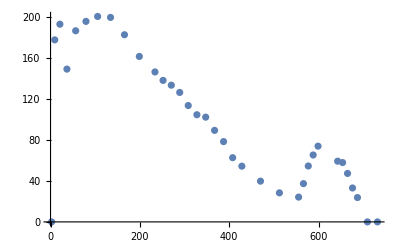

```mathematica
ListPlot[plot]
```

Теперь нам нужно провести наилучшую прямую через часть графика (МНК)

```mathematica
plotApproxS=QuantityMagnitude[plot]
```

{{5.68434×10^-14,Indeterminate},{2.36901,0.},{9.41134,177.702},{20.9414,192.976},{36.6759,149.15},{56.2649,186.579},{79.325,195.726},{105.467,200.55},{134.316,199.628},{165.526,182.707},{198.785,161.531},{233.82,146.376},{251.927,138.134},{270.391,133.456},{289.187,126.379},{308.292,113.597},{327.686,104.618},{347.348,102.244},{367.261,89.3445},{387.408,78.3885},{407.774,62.6838},{428.343,54.4023},{470.045,39.7754},{512.418,28.3463},{555.383,24.1999},{566.209,37.3435},{577.066,54.5654},{587.954,65.3183},{598.872,73.9374},{642.825,59.2699},{653.88,57.9269},{664.959,47.3098},{676.064,33.1194},{687.191,23.7862},{709.515,0.},{731.926,0.}}

Подправим значения

```mathematica
plotApproxS[[1,1]]=0;
plotApproxS[[1,2]]=0;
```

Интересующий нас интервал энергий: 130 - 520 кэВ

```mathematica
plotApproxS=plotApproxS[[9;;24]]
```

{{134.316,199.628},{165.526,182.707},{198.785,161.531},{233.82,146.376},{251.927,138.134},{270.391,133.456},{289.187,126.379},{308.292,113.597},{327.686,104.618},{347.348,102.244},{367.261,89.3445},{387.408,78.3885},{407.774,62.6838},{428.343,54.4023},{470.045,39.7754},{512.418,28.3463}}

```mathematica
plotApproxFunc=LinearModelFit[plotApproxS,x,x]
```

FittedModel[256.886-0.460457 x]

Совместим графики:

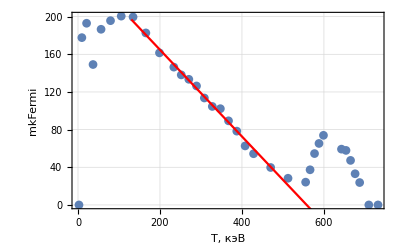

```mathematica
Show[ListPlot[plot,PlotTheme->"Detailed",Frame->True,FrameLabel->{"T, кэВ", "mkFermi"},PlotMarkers->Automatic],Plot[plotApproxFunc["BestFit"],{x,130,598},PlotStyle->Red]]
```

Найдем персечение полученной прямой с осью OX

```mathematica
(x/.Solve[y==plotApproxFunc["BestFit"],x][[1]])/.y-> 0
```

557.895